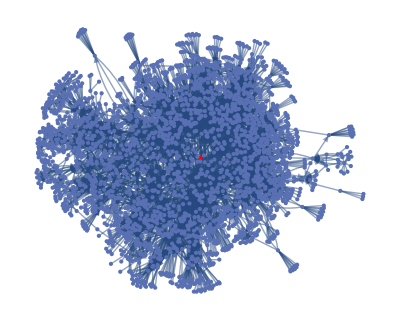

```mathematica
links=WikipediaData["PageRank","BacklinksRules","MaxLevelItems"->10,"MaxLevel"->4];
g=Graph[links,VertexLabels->Placed["Name",Tooltip],VertexStyle->{"PageRank"->Red}]
```

```mathematica
EdgeCount[g]
```

5920

```mathematica
VertexCount[g]
```

2657

```mathematica
hyperlinkmat =AdjacencyMatrix[links]//MatrixForm
```

(1)
 |  |  |  |

```mathematica
Export["/Users/zifeiyu/desktop/mat.mtx",hyperlinkmat,"MTX"]
```

/Users/zifeiyu/desktop/mat.mtx